```mathematica
Clear[a,p,q,x];
```

```mathematica
Import["C:\\Users\\jprasadh\\Downloads\\Experiment 9\\doubleslitdata.csv"];
```

```mathematica
singleslitdata={{0,0.1},{0,0.1},{0,0.1},{0,0.1},{0,0.1},{0,0.1},{0,0.1},{0,0.1},{0,0.1},{0,0.1},{0,0.1},{0,0.1},{0,0.1},{0,0.1},{-0.00010958,0.1},{-0.00010958,0.1},{-0.00010958,0.1},{-0.00010958,0.1},{-0.00016437,0.1},{-0.00021917,0.1},{-0.00032875,0.1},{-0.00043833,0.1},{-0.00076708,0.1},{-0.001,0.1},{-0.0014,0.1},{-0.0015,0.1},{-0.0018,0.1},{-0.002,0.1},{-0.0021,0.1},{-0.0022,0.1},{-0.0023,0.1},{-0.0024,0.1},{-0.0026,0.1},{-0.0028,0.1},{-0.0031,0.1},{-0.0033,0.1},{-0.0035,0.1},{-0.0036,0.1},{-0.0038,0.1},{-0.0041,0.1},{-0.0042,0.1},{-0.0044,0.1},{-0.0046,0.1},{-0.0049,0.1},{-0.0052,0.1},{-0.0055,0.1},{-0.0059,0.1},{-0.0062,0.1},{-0.0065,0.1},{-0.0067,0.1},{-0.0068,0.1},{-0.007,0.1},{-0.007,0.1},{-0.0071,0.1},{-0.0073,0.1},{-0.0075,0.1},{-0.0077,0.1},{-0.0079,0.1},{-0.0081,0.1},{-0.0084,0.1},{-0.0088,0.1},{-0.009,0.1},{-0.0093,0.1},{-0.0095,0.1},{-0.0098,0.1},{-0.0101,0.1},{-0.0103,0.1},{-0.0105,0.1},{-0.0107,0.1},{-0.0109,0.1},{-0.0111,0.1},{-0.0113,0.2},{-0.0113,0.2},{-0.0115,0.2},{-0.0117,0.2},{-0.012,0.2},{-0.0123,0.2},{-0.0126,0.2},{-0.0129,0.2},{-0.0133,0.1},{-0.0135,0.1},{-0.0137,0.1},{-0.0138,0.1},{-0.014,0.1},{-0.0141,0.1},{-0.0143,0.1},{-0.0145,0.1},{-0.0146,0.1},{-0.0147,0.1},{-0.0149,0.1},{-0.0151,0.1},{-0.0153,0.1},{-0.0156,0.1},{-0.0158,0.1},{-0.016,0.1},{-0.0162,0.1},{-0.0163,0.1},{-0.0164,0.1},{-0.0165,0.1},{-0.0166,0.1},{-0.0167,0.1},{-0.0168,0.1},{-0.0171,0.1},{-0.0174,0.1},{-0.0177,0.2},{-0.018,0.2},{-0.0182,0.2},{-0.0185,0.2},{-0.0188,0.3},{-0.0192,0.3},{-0.0195,0.3},{-0.0198,0.3},{-0.0199,0.3},{-0.0201,0.3},{-0.0202,0.3},{-0.0203,0.3},{-0.0204,0.3},{-0.0205,0.3},{-0.0206,0.3},{-0.0207,0.3},{-0.0208,0.3},{-0.0209,0.2},{-0.0211,0.2},{-0.0214,0.2},{-0.0216,0.2},{-0.0219,0.2},{-0.0222,0.1},{-0.0225,0.1},{-0.0228,0.2},{-0.0231,0.2},{-0.0232,0.2},{-0.0234,0.2},{-0.0236,0.2},{-0.0237,0.3},{-0.0238,0.3},{-0.024,0.4},{-0.0241,0.4},{-0.0243,0.5},{-0.0244,0.6},{-0.0245,0.7},{-0.0247,0.8},{-0.0248,0.9},{-0.025,1},{-0.0253,1.2},{-0.0255,1.5},{-0.0256,1.6},{-0.0258,1.8},{-0.0259,1.9},{-0.026,2},{-0.0261,2.1},{-0.0264,2.3},{-0.0266,2.4},{-0.0268,2.6},{-0.0268,2.8},{-0.0269,2.9},{-0.027,3},{-0.0271,3.1},{-0.0272,3.3},{-0.0274,3.5},{-0.0276,3.7},{-0.0277,3.9},{-0.0279,4.2},{-0.0281,4.5},{-0.0281,4.6},{-0.0281,4.6},{-0.0282,4.6},{-0.0282,4.7},{-0.0284,4.8},{-0.0285,4.9},{-0.0287,5},{-0.0289,5.2},{-0.0292,5.3},{-0.0294,5.5},{-0.0295,5.6},{-0.0296,5.6},{-0.0296,5.6},{-0.0297,5.6},{-0.0299,5.6},{-0.03,5.5},{-0.03,5.5},{-0.03,5.5},{-0.0301,5.5},{-0.0302,5.6},{-0.0304,5.6},{-0.0305,5.6},{-0.0307,5.5},{-0.0309,5.5},{-0.0311,5.5},{-0.0313,5.3},{-0.0316,5.1},{-0.0318,4.9},{-0.0322,4.5},{-0.0325,4.2},{-0.0328,3.9},{-0.0331,3.7},{-0.0332,3.4},{-0.0332,3.4},{-0.0332,3.3},{-0.0333,3.3},{-0.0334,3.2},{-0.0335,3.1},{-0.0335,3},{-0.0335,3},{-0.0335,3},{-0.0338,2.9},{-0.0343,2.5},{-0.0348,1.7},{-0.035,1.3},{-0.0352,1.1},{-0.0354,0.9},{-0.0357,0.8},{-0.0359,0.6},{-0.0361,0.5},{-0.0362,0.5},{-0.0363,0.4},{-0.0363,0.4},{-0.0363,0.4},{-0.0363,0.4},{-0.0363,0.4},{-0.0364,0.4},{-0.0365,0.3},{-0.0368,0.3},{-0.0369,0.2},{-0.0372,0.2},{-0.0375,0.1},{-0.0378,0.1},{-0.038,0.1},{-0.0381,0.1},{-0.0384,0.1},{-0.0386,0.2},{-0.039,0.2},{-0.0393,0.2},{-0.0396,0.2},{-0.0398,0.3},{-0.0399,0.3},{-0.0401,0.3},{-0.0404,0.3},{-0.0408,0.3},{-0.0411,0.3},{-0.0413,0.3},{-0.0416,0.3},{-0.042,0.3},{-0.0423,0.3},{-0.0424,0.2},{-0.0424,0.2},{-0.0424,0.2},{-0.0424,0.2},{-0.0426,0.2},{-0.043,0.2},{-0.0434,0.2},{-0.0436,0.2},{-0.0438,0.1},{-0.0439,0.1},{-0.0441,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0442,0.1},{-0.0446,0.1},{-0.0453,0.1},{-0.0453,0.1},{-0.0453,0.1},{-0.0453,0.1},{-0.046,0.1},{-0.0473,0.1},{-0.0481,0.1},{-0.0482,0.1},{-0.0482,0.1},{-0.0482,0.1},{-0.0482,0.1},{-0.0483,0.1},{-0.0485,0.1},{-0.0487,0.1},{-0.0489,0.1},{-0.0494,0.1},{-0.05,0.1},{-0.0505,0.1},{-0.0509,0.1},{-0.0512,0.1},{-0.0516,0.1},{-0.0521,0.1},{-0.0524,0.1},{-0.0527,0.1},{-0.0529,0.1},{-0.0531,0.1},{-0.0535,0.1},{-0.0539,0.1},{-0.0543,0.1},{-0.0545,0.1},{-0.0548,0.1},{-0.0552,0.1},{-0.0557,0.1},{-0.0562,0.1},{-0.0565,0.1},{-0.057,0.1},{-0.0574,0.1},{-0.0579,0.1},{-0.0584,0.1},{-0.0587,0.1},{-0.0589,0.1},{-0.059,0.1},{-0.0592,0.1},{-0.0594,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1},{-0.0597,0.1}};
adjsingleslitdata={{0.0302311,0.1},{0.0302311,0.1},{0.0302311,0.1},{0.0302311,0.1},{0.0302311,0.1},{0.0302311,0.1},{0.0302311,0.1},{0.0302311,0.1},{0.0302311,0.1},{0.0302311,0.1},{0.0302311,0.1},{0.0302311,0.1},{0.0302311,0.1},{0.0302311,0.1},{0.03012152,0.1},{0.03012152,0.1},{0.03012152,0.1},{0.03012152,0.1},{0.03006673,0.1},{0.03001193,0.1},{0.02990235,0.1},{0.02979277,0.1},{0.02946402,0.1},{0.0292311,0.1},{0.0288311,0.1},{0.0287311,0.1},{0.0284311,0.1},{0.0282311,0.1},{0.0281311,0.1},{0.0280311,0.1},{0.0279311,0.1},{0.0278311,0.1},{0.0276311,0.1},{0.0274311,0.1},{0.0271311,0.1},{0.0269311,0.1},{0.0267311,0.1},{0.0266311,0.1},{0.0264311,0.1},{0.0261311,0.1},{0.0260311,0.1},{0.0258311,0.1},{0.0256311,0.1},{0.0253311,0.1},{0.0250311,0.1},{0.0247311,0.1},{0.0243311,0.1},{0.0240311,0.1},{0.0237311,0.1},{0.0235311,0.1},{0.0234311,0.1},{0.0232311,0.1},{0.0232311,0.1},{0.0231311,0.1},{0.0229311,0.1},{0.0227311,0.1},{0.0225311,0.1},{0.0223311,0.1},{0.0221311,0.1},{0.0218311,0.1},{0.0214311,0.1},{0.0212311,0.1},{0.0209311,0.1},{0.0207311,0.1},{0.0204311,0.1},{0.0201311,0.1},{0.0199311,0.1},{0.0197311,0.1},{0.0195311,0.1},{0.0193311,0.1},{0.0191311,0.1},{0.0189311,0.2},{0.0189311,0.2},{0.0187311,0.2},{0.0185311,0.2},{0.0182311,0.2},{0.0179311,0.2},{0.0176311,0.2},{0.0173311,0.2},{0.0169311,0.1},{0.0167311,0.1},{0.0165311,0.1},{0.0164311,0.1},{0.0162311,0.1},{0.0161311,0.1},{0.0159311,0.1},{0.0157311,0.1},{0.0156311,0.1},{0.0155311,0.1},{0.0153311,0.1},{0.0151311,0.1},{0.0149311,0.1},{0.0146311,0.1},{0.0144311,0.1},{0.0142311,0.1},{0.0140311,0.1},{0.0139311,0.1},{0.0138311,0.1},{0.0137311,0.1},{0.0136311,0.1},{0.0135311,0.1},{0.0134311,0.1},{0.0131311,0.1},{0.0128311,0.1},{0.0125311,0.2},{0.0122311,0.2},{0.0120311,0.2},{0.0117311,0.2},{0.0114311,0.3},{0.0110311,0.3},{0.0107311,0.3},{0.0104311,0.3},{0.0103311,0.3},{0.0101311,0.3},{0.0100311,0.3},{0.0099311,0.3},{0.0098311,0.3},{0.0097311,0.3},{0.0096311,0.3},{0.0095311,0.3},{0.0094311,0.3},{0.0093311,0.2},{0.0091311,0.2},{0.0088311,0.2},{0.0086311,0.2},{0.0083311,0.2},{0.0080311,0.1},{0.0077311,0.1},{0.0074311,0.2},{0.0071311,0.2},{0.0070311,0.2},{0.0068311,0.2},{0.0066311,0.2},{0.0065311,0.3},{0.0064311,0.3},{0.0062311,0.4},{0.0061311,0.4},{0.0059311,0.5},{0.0058311,0.6},{0.0057311,0.7},{0.0055311,0.8},{0.0054311,0.9},{0.0052311,1},{0.0049311,1.2},{0.0047311,1.5},{0.0046311,1.6},{0.0044311,1.8},{0.0043311,1.9},{0.0042311,2},{0.0041311,2.1},{0.0038311,2.3},{0.0036311,2.4},{0.0034311,2.6},{0.0034311,2.8},{0.0033311,2.9},{0.0032311,3},{0.0031311,3.1},{0.0030311,3.3},{0.0028311,3.5},{0.0026311,3.7},{0.0025311,3.9},{0.0023311,4.2},{0.0021311,4.5},{0.0021311,4.6},{0.0021311,4.6},{0.0020311,4.6},{0.0020311,4.7},{0.0018311,4.8},{0.0017311,4.9},{0.0015311,5},{0.0013311,5.2},{0.0010311,5.3},{0.0008311,5.5},{0.0007311,5.6},{0.0006311,5.6},{0.0006311,5.6},{0.0005311,5.6},{0.0003311,5.6},{0.0002311,5.5},{0.0002311,5.5},{0.0002311,5.5},{0.0001311,5.5},{0.0000311,5.6},{-0.0001689,5.6},{-0.0002689,5.6},{-0.0004689,5.5},{-0.0006689,5.5},{-0.0008689,5.5},{-0.0010689,5.3},{-0.0013689,5.1},{-0.0015689,4.9},{-0.0019689,4.5},{-0.0022689,4.2},{-0.0025689,3.9},{-0.0028689,3.7},{-0.0029689,3.4},{-0.0029689,3.4},{-0.0029689,3.3},{-0.0030689,3.3},{-0.0031689,3.2},{-0.0032689,3.1},{-0.0032689,3},{-0.0032689,3},{-0.0032689,3},{-0.0035689,2.9},{-0.0040689,2.5},{-0.0045689,1.7},{-0.0047689,1.3},{-0.0049689,1.1},{-0.0051689,0.9},{-0.0054689,0.8},{-0.0056689,0.6},{-0.0058689,0.5},{-0.0059689,0.5},{-0.0060689,0.4},{-0.0060689,0.4},{-0.0060689,0.4},{-0.0060689,0.4},{-0.0060689,0.4},{-0.0061689,0.4},{-0.0062689,0.3},{-0.0065689,0.3},{-0.0066689,0.2},{-0.0069689,0.2},{-0.0072689,0.1},{-0.0075689,0.1},{-0.0077689,0.1},{-0.0078689,0.1},{-0.0081689,0.1},{-0.0083689,0.2},{-0.0087689,0.2},{-0.0090689,0.2},{-0.0093689,0.2},{-0.0095689,0.3},{-0.0096689,0.3},{-0.0098689,0.3},{-0.0101689,0.3},{-0.0105689,0.3},{-0.0108689,0.3},{-0.0110689,0.3},{-0.0113689,0.3},{-0.0117689,0.3},{-0.0120689,0.3},{-0.0121689,0.2},{-0.0121689,0.2},{-0.0121689,0.2},{-0.0121689,0.2},{-0.0123689,0.2},{-0.0127689,0.2},{-0.0131689,0.2},{-0.0133689,0.2},{-0.0135689,0.1},{-0.0136689,0.1},{-0.0138689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0139689,0.1},{-0.0143689,0.1},{-0.0150689,0.1},{-0.0150689,0.1},{-0.0150689,0.1},{-0.0150689,0.1},{-0.0157689,0.1},{-0.0170689,0.1},{-0.0178689,0.1},{-0.0179689,0.1},{-0.0179689,0.1},{-0.0179689,0.1},{-0.0179689,0.1},{-0.0180689,0.1},{-0.0182689,0.1},{-0.0184689,0.1},{-0.0186689,0.1},{-0.0191689,0.1},{-0.0197689,0.1},{-0.0202689,0.1},{-0.0206689,0.1},{-0.0209689,0.1},{-0.0213689,0.1},{-0.0218689,0.1},{-0.0221689,0.1},{-0.0224689,0.1},{-0.0226689,0.1},{-0.0228689,0.1},{-0.0232689,0.1},{-0.0236689,0.1},{-0.0240689,0.1},{-0.0242689,0.1},{-0.0245689,0.1},{-0.0249689,0.1},{-0.0254689,0.1},{-0.0259689,0.1},{-0.0262689,0.1},{-0.0267689,0.1},{-0.0271689,0.1},{-0.0276689,0.1},{-0.0281689,0.1},{-0.0284689,0.1},{-0.0286689,0.1},{-0.0287689,0.1},{-0.0289689,0.1},{-0.0291689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1},{-0.0294689,0.1}};
```

```mathematica
doubleslitdata={{0,0.1},{0,0.1},{0,0.1},{-0.00010958,0.1},{-0.00016437,0.1},{-0.00021917,0.1},{-0.00027396,0.1},{-0.00054792,0.1},{-0.0006575,0.1},{-0.00076708,0.1},{-0.00087667,0.1},{-0.00098625,0.1},{-0.0011,0.1},{-0.0012,0.1},{-0.0014,0.1},{-0.0015,0.1},{-0.0016,0.1},{-0.0017,0.1},{-0.0018,0.1},{-0.002,0.1},{-0.002,0.1},{-0.0021,0.1},{-0.0022,0.1},{-0.0023,0.1},{-0.0024,0.1},{-0.0026,0.1},{-0.0028,0.1},{-0.0031,0.2},{-0.0032,0.4},{-0.0033,0.4},{-0.0034,0.4},{-0.0035,0.3},{-0.0036,0.2},{-0.0037,0.1},{-0.0038,0.1},{-0.0039,0.2},{-0.0041,0.4},{-0.0042,0.6},{-0.0043,0.8},{-0.0045,0.9},{-0.0047,0.7},{-0.0048,0.5},{-0.0049,0.3},{-0.005,0.1},{-0.0051,0.1},{-0.0052,0.1},{-0.0053,0.2},{-0.0054,0.3},{-0.0055,0.6},{-0.0056,0.9},{-0.0056,1},{-0.0058,1.1},{-0.0058,1.1},{-0.0059,1.1},{-0.0059,1},{-0.006,0.8},{-0.006,0.6},{-0.0061,0.4},{-0.0061,0.3},{-0.0062,0.1},{-0.0063,0.1},{-0.0064,0.2},{-0.0066,0.6},{-0.0066,0.9},{-0.0067,0.9},{-0.0068,0.9},{-0.007,0.8},{-0.0072,0.5},{-0.0075,0.2},{-0.0078,0.3},{-0.0081,0.5},{-0.0083,0.4},{-0.0085,0.2},{-0.0087,0.2},{-0.0088,0.1},{-0.0089,0.1},{-0.0091,0.2},{-0.0093,0.3},{-0.0094,0.4},{-0.0095,0.4},{-0.0096,0.4},{-0.0096,0.3},{-0.0098,0.2},{-0.0098,0.2},{-0.0099,0.1},{-0.0099,0.2},{-0.0099,0.2},{-0.01,0.3},{-0.0101,0.4},{-0.0101,0.7},{-0.0102,0.9},{-0.0104,1.3},{-0.0105,1.7},{-0.0106,1.8},{-0.0107,1.6},{-0.0108,1.1},{-0.011,0.5},{-0.0111,0.3},{-0.0113,1},{-0.0114,2.5},{-0.0115,3.9},{-0.0116,4.8},{-0.0117,5.1},{-0.0118,5},{-0.0119,4.6},{-0.0119,3.8},{-0.0121,2.7},{-0.0122,1.2},{-0.0123,0.4},{-0.0124,0.4},{-0.0124,1.2},{-0.0126,3.3},{-0.0127,7.2},{-0.0128,9.8},{-0.0128,10.1},{-0.0129,9.7},{-0.013,8.1},{-0.0131,5.7},{-0.0132,3.6},{-0.0133,1.4},{-0.0134,0.5},{-0.0135,1.4},{-0.0138,6},{-0.0139,13.1},{-0.014,15.6},{-0.0141,14.5},{-0.0142,12},{-0.0144,6.4},{-0.0145,1.6},{-0.0146,0.5},{-0.0148,1.5},{-0.015,5.2},{-0.015,9.1},{-0.0151,13.1},{-0.0153,17.6},{-0.0155,19.7},{-0.0156,16.4},{-0.0156,14},{-0.0158,8.2},{-0.0159,1.1},{-0.0159,1.2},{-0.016,1.9},{-0.0161,5.2},{-0.0162,12.5},{-0.0163,20.2},{-0.0164,21.8},{-0.0165,20},{-0.0166,15.4},{-0.0168,8.6},{-0.0168,3},{-0.0168,2.3},{-0.0168,2.1},{-0.017,1.4},{-0.0173,5.6},{-0.0175,17.2},{-0.0176,20},{-0.0178,17.4},{-0.0179,11.5},{-0.018,5.1},{-0.0182,2},{-0.0184,0.9},{-0.0185,3.3},{-0.0186,7.6},{-0.0187,9.8},{-0.0187,12.5},{-0.0188,14.4},{-0.019,15.5},{-0.0191,12.7},{-0.0193,7.3},{-0.0194,2},{-0.0196,0.9},{-0.0197,5.2},{-0.0198,9.1},{-0.0198,9.7},{-0.0198,9.8},{-0.0199,9.9},{-0.0201,9.2},{-0.0204,4.4},{-0.0204,1.3},{-0.0204,1.1},{-0.0204,1},{-0.0204,1},{-0.0207,0.7},{-0.0208,2.3},{-0.0208,3.7},{-0.021,3.9},{-0.0213,4.6},{-0.0213,4.2},{-0.0213,4.2},{-0.0213,4.1},{-0.0213,4.1},{-0.0216,3.6},{-0.0219,1.4},{-0.0219,0.4},{-0.0219,0.4},{-0.0219,0.3},{-0.0219,0.3},{-0.0221,0.4},{-0.0225,1.4},{-0.0225,1.5},{-0.0225,1.3},{-0.0225,1.2},{-0.0228,1.1},{-0.0231,0.3},{-0.0232,0.4},{-0.0232,0.4},{-0.0235,0.4},{-0.0235,0.4},{-0.0235,0.4},{-0.0238,0.3},{-0.0241,0.1},{-0.0241,0.1},{-0.0242,0.1},{-0.0244,0.2},{-0.0246,0.3},{-0.0248,0.4},{-0.0249,0.5},{-0.025,0.5},{-0.025,0.5},{-0.0253,0.5},{-0.0254,0.3},{-0.0254,0.2},{-0.0255,0.1},{-0.0256,0.1},{-0.026,0.3},{-0.0261,0.9},{-0.0261,1},{-0.0261,1},{-0.0261,1},{-0.0261,1},{-0.0261,1},{-0.0261,1},{-0.0261,1},{-0.0261,1},{-0.0264,0.9},{-0.0266,0.3},{-0.0267,0.2},{-0.0267,0.3},{-0.027,0.5},{-0.0271,1.1},{-0.0272,1.2},{-0.0272,1.2},{-0.0275,1},{-0.0277,0.4},{-0.0277,0.2},{-0.0279,0.2},{-0.0281,0.2},{-0.0281,0.3},{-0.0284,0.4},{-0.0286,0.9},{-0.0288,0.9},{-0.0289,0.7},{-0.0289,0.5},{-0.0289,0.4},{-0.0289,0.4},{-0.0289,0.4},{-0.0293,0.2},{-0.0295,0.3},{-0.0295,0.4},{-0.0297,0.5},{-0.0299,0.4},{-0.0302,0.2},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1},{-0.0302,0.1}};
adjdoubleslitdata={{0.0164,0.024536713},{0.0164,0.024536713},{0.0164,0.024536713},{0.01629042,0.024536713},{0.01623563,0.024536713},{0.01618083,0.024536713},{0.01612604,0.024536713},{0.01585208,0.024536713},{0.0157425,0.024536713},{0.01563292,0.024536713},{0.01552333,0.024536713},{0.01541375,0.024536713},{0.0153,0.024536713},{0.0152,0.024536713},{0.015,0.024536713},{0.0149,0.024536713},{0.0148,0.024536713},{0.0147,0.024536713},{0.0146,0.024536713},{0.0144,0.024536713},{0.0144,0.024536713},{0.0143,0.024536713},{0.0142,0.024536713},{0.0141,0.024536713},{0.014,0.024536713},{0.0138,0.024536713},{0.0136,0.024536713},{0.0133,0.049073427},{0.0132,0.098146853},{0.0131,0.098146853},{0.013,0.098146853},{0.0129,0.07361014},{0.0128,0.049073427},{0.0127,0.024536713},{0.0126,0.024536713},{0.0125,0.049073427},{0.0123,0.098146853},{0.0122,0.14722028},{0.0121,0.196293706},{0.0119,0.22083042},{0.0117,0.171756993},{0.0116,0.122683567},{0.0115,0.07361014},{0.0114,0.024536713},{0.0113,0.024536713},{0.0112,0.024536713},{0.0111,0.049073427},{0.011,0.07361014},{0.0109,0.14722028},{0.0108,0.22083042},{0.0108,0.245367133},{0.0106,0.269903846},{0.0106,0.269903846},{0.0105,0.269903846},{0.0105,0.245367133},{0.0104,0.196293706},{0.0104,0.14722028},{0.0103,0.098146853},{0.0103,0.07361014},{0.0102,0.024536713},{0.0101,0.024536713},{0.01,0.049073427},{0.0098,0.14722028},{0.0098,0.22083042},{0.0097,0.22083042},{0.0096,0.22083042},{0.0094,0.196293706},{0.0092,0.122683567},{0.0089,0.049073427},{0.0086,0.07361014},{0.0083,0.122683567},{0.0081,0.098146853},{0.0079,0.049073427},{0.0077,0.049073427},{0.0076,0.024536713},{0.0075,0.024536713},{0.0073,0.049073427},{0.0071,0.07361014},{0.007,0.098146853},{0.0069,0.098146853},{0.0068,0.098146853},{0.0068,0.07361014},{0.0066,0.049073427},{0.0066,0.049073427},{0.0065,0.024536713},{0.0065,0.049073427},{0.0065,0.049073427},{0.0064,0.07361014},{0.0063,0.098146853},{0.0063,0.171756993},{0.0062,0.22083042},{0.006,0.318977273},{0.0059,0.417124127},{0.0058,0.44166084},{0.0057,0.392587414},{0.0056,0.269903846},{0.0054,0.122683567},{0.0053,0.07361014},{0.0051,0.245367133},{0.005,0.613417834},{0.0049,0.95693182},{0.0048,1.17776224},{0.0047,1.25137238},{0.0046,1.226835667},{0.0045,1.128688814},{0.0045,0.932395106},{0.0043,0.66249126},{0.0042,0.29444056},{0.0041,0.098146853},{0.004,0.098146853},{0.004,0.29444056},{0.0038,0.80971154},{0.0037,1.766643361},{0.0036,2.404597906},{0.0036,2.478208047},{0.0035,2.380061193},{0.0034,1.98747378},{0.0033,1.39859266},{0.0032,0.88332168},{0.0031,0.343513987},{0.003,0.122683567},{0.0029,0.343513987},{0.0026,1.4722028},{0.0025,3.214309447},{0.0024,3.82772728},{0.0023,3.557823434},{0.0022,2.9444056},{0.002,1.570349653},{0.0019,0.392587414},{0.0018,0.122683567},{0.0016,0.368050701},{0.0014,1.275909094},{0.0014,2.232840913},{0.0013,3.214309447},{0.0011,4.318461547},{0.0009,4.833732527},{0.0008,4.024020987},{0.0008,3.435139867},{0.0006,2.012010494},{0.0005,0.269903846},{0.0005,0.29444056},{0.0004,0.466197554},{0.0003,1.275909094},{0.0002,3.067089167},{0.0001,4.956416094},{0,5.349003507},{-0.0001,4.907342667},{-0.0002,3.778653853},{-0.0004,2.110157347},{-0.0004,0.7361014},{-0.0004,0.564344407},{-0.0004,0.51527098},{-0.0006,0.343513987},{-0.0009,1.374055947},{-0.0011,4.220314694},{-0.0012,4.907342667},{-0.0014,4.26938812},{-0.0015,2.821722034},{-0.0016,1.25137238},{-0.0018,0.490734267},{-0.002,0.22083042},{-0.0021,0.80971154},{-0.0022,1.864790214},{-0.0023,2.404597906},{-0.0023,3.067089167},{-0.0024,3.53328672},{-0.0026,3.803190567},{-0.0027,3.116162593},{-0.0029,1.791180074},{-0.003,0.490734267},{-0.0032,0.22083042},{-0.0033,1.275909094},{-0.0034,2.232840913},{-0.0034,2.380061193},{-0.0034,2.404597906},{-0.0035,2.42913462},{-0.0037,2.257377627},{-0.004,1.079615387},{-0.004,0.318977273},{-0.004,0.269903846},{-0.004,0.245367133},{-0.004,0.245367133},{-0.0043,0.171756993},{-0.0044,0.564344407},{-0.0044,0.907858393},{-0.0046,0.95693182},{-0.0049,1.128688814},{-0.0049,1.03054196},{-0.0049,1.03054196},{-0.0049,1.006005246},{-0.0049,1.006005246},{-0.0052,0.88332168},{-0.0055,0.343513987},{-0.0055,0.098146853},{-0.0055,0.098146853},{-0.0055,0.07361014},{-0.0055,0.07361014},{-0.0057,0.098146853},{-0.0061,0.343513987},{-0.0061,0.368050701},{-0.0061,0.318977273},{-0.0061,0.29444056},{-0.0064,0.269903846},{-0.0067,0.07361014},{-0.0068,0.098146853},{-0.0068,0.098146853},{-0.0071,0.098146853},{-0.0071,0.098146853},{-0.0071,0.098146853},{-0.0074,0.07361014},{-0.0077,0.024536713},{-0.0077,0.024536713},{-0.0078,0.024536713},{-0.008,0.049073427},{-0.0082,0.07361014},{-0.0084,0.098146853},{-0.0085,0.122683567},{-0.0086,0.122683567},{-0.0086,0.122683567},{-0.0089,0.122683567},{-0.009,0.07361014},{-0.009,0.049073427},{-0.0091,0.024536713},{-0.0092,0.024536713},{-0.0096,0.07361014},{-0.0097,0.22083042},{-0.0097,0.245367133},{-0.0097,0.245367133},{-0.0097,0.245367133},{-0.0097,0.245367133},{-0.0097,0.245367133},{-0.0097,0.245367133},{-0.0097,0.245367133},{-0.0097,0.245367133},{-0.01,0.22083042},{-0.0102,0.07361014},{-0.0103,0.049073427},{-0.0103,0.07361014},{-0.0106,0.122683567},{-0.0107,0.269903846},{-0.0108,0.29444056},{-0.0108,0.29444056},{-0.0111,0.245367133},{-0.0113,0.098146853},{-0.0113,0.049073427},{-0.0115,0.049073427},{-0.0117,0.049073427},{-0.0117,0.07361014},{-0.012,0.098146853},{-0.0122,0.22083042},{-0.0124,0.22083042},{-0.0125,0.171756993},{-0.0125,0.122683567},{-0.0125,0.098146853},{-0.0125,0.098146853},{-0.0125,0.098146853},{-0.0129,0.049073427},{-0.0131,0.07361014},{-0.0131,0.098146853},{-0.0133,0.122683567},{-0.0135,0.098146853},{-0.0138,0.049073427},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713},{-0.0138,0.024536713}};
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 5.63053 | 0.0162637 | 346.203 | 2.340155445521×10^-483
p | 398.186 | 1.19948 | 331.966 | 2.429473909823×10^-476
q | -0.0302311 | 0.0000101985 | -2964.26 | 4.532678984283×10^-843

5.63053 Sinc[398.186 (0.0302311+x)]^2

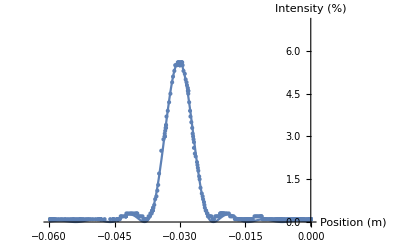

```mathematica
uaIntensity=NonlinearModelFit[singleslitdata,a (Sinc[p(x-q)])^2 ,{a,p,q},x];
uaIntensity["ParameterTable"]
Normal[uaIntensity]
Show[Plot[uaIntensity[x],{x,-.06, 0},PlotRange->{0,7}],ListPlot[singleslitdata],AxesLabel->{"Position (m)","Intensity (%)"}]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 5.63053 | 0.0161632 | 348.355 | 1.997840574066×10^-485
p | 398.186 | 1.19788 | 332.41 | 1.409028292995×10^-477

5.63053 Sinc[398.186 x]^2

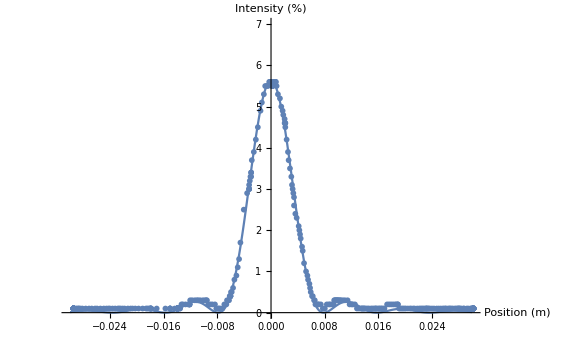

```mathematica
Intensity=NonlinearModelFit[adjsingleslitdata,a (Sinc[p * x])^2 ,{a,p},x];
Intensity["ParameterTable"]
Normal[Intensity]
Show[Plot[Intensity[x],{x,-.03, 0.03},PlotRange->{0,7}],ListPlot[adjsingleslitdata],AxesLabel->{"Position (m)","Intensity (%)"}]
```

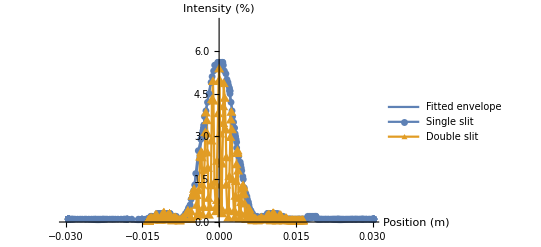

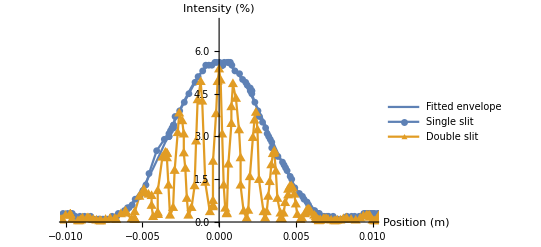

```mathematica
Show[Plot[Intensity[x],{x,-.03, 0.03},PlotRange->{0,7},PlotLegends->{"Fitted envelope"}],ListPlot[{adjsingleslitdata,adjdoubleslitdata},PlotMarkers->{{●,7},{▲,12}},PlotLegends->{"Single slit","Double slit"},Joined->True,PlotRange->{0,7}],AxesLabel->{"Position (m)","Intensity (%)"}]

Show[Plot[Intensity[x],{x,-.01, 0.01},PlotRange->{0,7},PlotLegends->{"Fitted envelope"}],ListPlot[{adjsingleslitdata,adjdoubleslitdata},PlotMarkers->{{●,7},{▲,12}},PlotLegends->{"Single slit","Double slit"},Joined->True,PlotRange->{0,7}],AxesLabel->{"Position (m)","Intensity (%)"}]
```

```mathematica
Import["C:\\Users\\jprasadh\\Downloads\\Experiment 9\\fopeakwidthdata.csv"];
ObsFOPeakWidthData={{2,0.0026},{3,0.0017},{4,0.0014},{5,0.00091}};
```

```mathematica
lambda=650*10^-9;
L=.99;
d=.125*10^-3;
PW[n_]:=(2.8 lambda L)/(Pi n d);
```

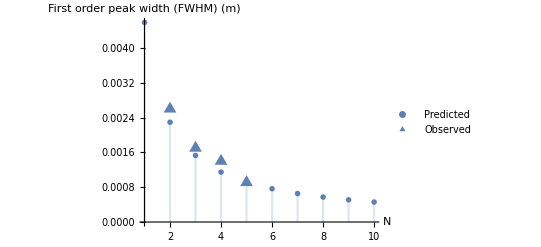

```mathematica
Show[DiscretePlot[PW[n],{n,1,10},PlotMarkers->{●,5},PlotLegends->{"Predicted"}],ListPlot[ObsFOPeakWidthData,PlotMarkers->{▲,15},PlotLegends->{"Observed"},Joined->False],AxesLabel->{"N","First order peak width (FWHM) (m)"}]
```